```mathematica
f[x_]:=x^3-1;
```

```mathematica
Nest[N[#-f[#]/f'[#]]&,1+2ⅈ,10]
```

0.290239+0.63153 ⅈ

```mathematica
Nest[N[#-f[#]/f'[#]]&,1-2ⅈ,10]
```

0.290239-0.63153 ⅈ

```mathematica
Nest[N[#-f[#]/f'[#]]&,1+ⅈ,10]
```

1.+0. ⅈ

```mathematica
SolucionFinal[z_]:=Piecewise[{{Green,Re[z]≥0},{Red,Re[z]<0&&Im[z]≥0},{Blue,Re[z]<0&&Im[z]<0}}];
```

Paso 1: Generar una tabla de números complejos que serán nuestros valores iniciales

```mathematica
iniciales = Table[re+ⅈ im,{re,-2,2,0.05},{im,-2,2,0.05}];
```

```mathematica
MatrixForm[iniciales]
```

(-2.-2. ⅈ | -2.-1.1 ⅈ | -2.-0.2 ⅈ | -2.+0.7 ⅈ | -2.+1.6 ⅈ
-1.1-2. ⅈ | -1.1-1.1 ⅈ | -1.1-0.2 ⅈ | -1.1+0.7 ⅈ | -1.1+1.6 ⅈ
-0.2-2. ⅈ | -0.2-1.1 ⅈ | -0.2-0.2 ⅈ | -0.2+0.7 ⅈ | -0.2+1.6 ⅈ
0.7-2. ⅈ | 0.7-1.1 ⅈ | 0.7-0.2 ⅈ | 0.7+0.7 ⅈ | 0.7+1.6 ⅈ
1.6-2. ⅈ | 1.6-1.1 ⅈ | 1.6-0.2 ⅈ | 1.6+0.7 ⅈ | 1.6+1.6 ⅈ)

Vamos a variar los valores iniciales del mapeo

```mathematica
NewtonRhapson[x0_]:=Quiet@Nest[N[#-f[#]/f'[#]]&,x0,10];
```

```mathematica
solutions  = Map[NewtonRhapson,iniciales,{2}];
```

```mathematica
colores = Map[SolucionFinal,solutions,{2}];
```

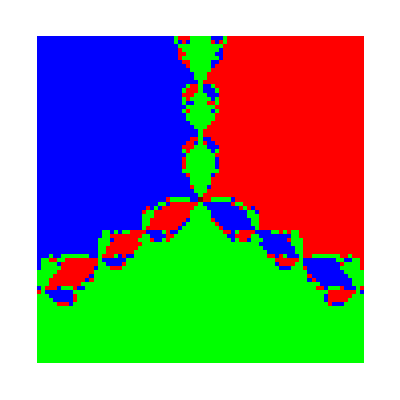

```mathematica
ArrayPlot[colores]
```